InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Gerade & remote

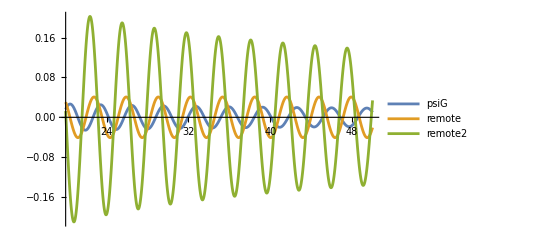

```mathematica
(* Upper Limit for integration *)
limit = 10;

(* Reduced Mass *)
μ=1835;
Subscript[m, p]=1836;
hbar= 1;  
c=137 ;(*SpeedOfLight, atomic units*)
 
vSg1Data = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx"];
vSu1Data = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx"];

maxR = 10;

(* Wave function outside scattering region *)
psiRemote[r_,k_,m_, delta_]:=(Cos[k r-Pi(m+1/2)+delta]);
psiRemote2[r_,k_,m_, delta_]:=Cos[delta]BesselJ[m,k r]+Sin[delta]BesselY[m, k r];

intPsiRemote := NIntegrate[(psiRemote[r,2,0, 0])^2, {r,1,50}];
intPsiRemote2 := NIntegrate[(psiRemote2[r,2,0, 0])^2, {r,1,50}];

(* potential in the scattering region *)
vGerade:=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}]];
vUngerade :=Interpolation[Transpose[{vSu1Data[[All,1]],vSu1Data[[All,3]]}]];

(* Wave function in the scatterin region *)
m=0;
k = 1;
geradeSol = 
NDSolve[{1/r D[r D [psiG[r],r],r]+(k^2-2vGerade[r]-m^2/r^2)psiG[r]==0,psiG[0.1] ==0,psiG'[0.1]==1},psiG[r],{r,0.1,50}];
unGeradeSol = 
First[NDSolve[{1/r D[r D [psiU[r],r],r]+(k^2-2vUngerade[r]-m^2/r^2)psiU[r]==0,psiU[0.1] ==0,psiU'[0.1]==1},psiU[r],{r,0.1,50}]];

Print["Gerade & remote"];

Plot[{psiG[r] /. geradeSol,psiRemote[r,2,0,0]/intPsiRemote,psiRemote2[r,2,0,0]/intPsiRemote2}, {r,20,50}, PlotLegends->{"psiG", "remote","remote2"}]
```

(-BesselJ[1,1] Cos[1]-BesselY[1,1] Sin[1])/(BesselJ[0,1] Cos[1]+BesselY[0,1] Sin[1])

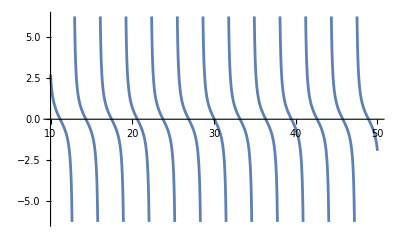

-Graphics-

```mathematica
(* Logarithmic derivative of the solution in the far region *)
fRemoteLogD[r_,k_,m_, delta_]:=(Cos[delta]D[BesselJ[m,k r],r]+Sin[delta]D[BesselY[m, k r],r])/(Cos[delta]BesselJ[m,k r]+Sin[delta]BesselY[m, k r]) //Evaluate;
(* Logarithmic derivative of the solution in the scattering region *)
(*fGeradeD:=D[psiG[r] ,r]/(psiG[r] /. geradeSol );*)
fRemoteLogD[1,1,0, 1] // Evaluate

Plot[ fRemoteLogD[r,1,0, 1],{r,10,50}]

fGeradeD=D[psiG[r]/.geradeSol,r];

logfGeradeD =D[psiG[r]/.geradeSol,r]/(psiG[r]/.geradeSol);


(*Plot[logfGeradeD /.x->r,{r,10,50}]*)
```